## Figure 1

Evaluate notebook to generate plots for Fig. 1A-D

```mathematica
Clear["Global`*"]; 
precision=30;
$MinPrecision=precision;
SetDirectory[NotebookDirectory[]];
```

### Statics

```mathematica
getPositions[pop0_]:=
Block[{m0,list,extendedPop},
m0=Length[pop0];
extendedPop=Join[{0},pop0];
Table[{Total[extendedPop[[1;;i-1]]],Total[extendedPop[[1;;i]]]},{i,2,m0+1}]
];

getConcentration[n_,nutrient_]:=
Block[{i,m0,c,dc,m,cSys,cSysWrap,cSystem,dcSys,dcSysWrap,dcSystem,totalcSys,vars,aVars,bVars,z},
m0=Length[n];
aVars=ToExpression[Table["a"<>IntegerString[k],{k,m0}]];
bVars=ToExpression[Table["b"<>IntegerString[k],{k,m0}]];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
dc[a_,b_,α_,θ_]:=Sqrt[α/d]*(a*E^(Sqrt[α/d]*θ)-b*E^(-Sqrt[α/d]*θ));

(*  Create a system of eqs for c(θ) in each region *)
cSys=Table[c[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==c[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
cSysWrap=c[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==c[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
cSystem=Join[cSys,{cSysWrap}];

(*do the same thing for the derivatives of c(θ)*)
dcSys=Table[dc[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==dc[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
dcSysWrap=dc[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==dc[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
dcSystem=Join[dcSys,{dcSysWrap}];

totalcSys=Join[cSystem,dcSystem];
vars=Table[{aVars[[i]],bVars[[i]]},{i,m0}]//Flatten;
{z,m}=CoefficientArrays[totalcSys,vars];
LinearSolve[m,-z]  
];
(*returns {a1,b1,a2,b2...}: in a region σ c_i=a*E^(a*θ/d)+b*E^(-a*θ/d)+si/αi. *)

fullConcentration[n_,nutrient_]:=
Block[{a,b,c,coeff,positions,pieces,conditions,fullC},
coeff=getConcentration[n,nutrient];
positions=getPositions[n];
a=Table[coeff[[2*i-1]],{i,m}];
b=Table[coeff[[2*i]],{i,m}];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
pieces=Table[c[a[[j]],b[[j]],α[[j,nutrient]],theta-positions[[j,1]]],{j,m}];
conditions=Table[positions[[i,1]]<theta<=positions[[i,2]],{i,m}];
fullC=Piecewise[Transpose[{pieces,conditions}]]
];
```

### Define some constants

```mathematica
supply=1;  (*total nutrient supply*)
δ=supply;
e=1;             (* total enzyme budget*)

steps=1200;
```

### Numeric parameters

```mathematica
d=1; //N(*diffusion coefficient*)
l=20;
s={.25,.45,.3};
p=Length[s];
SeedRandom[28];
```

```mathematica
m=10;
randomStrats[number_]:=RandomPoint[Simplex[e*IdentityMatrix[p]],number];
α=randomStrats[m];
```

```mathematica
α[[3,2]]+=.1;
α[[3,1]]-=.1;
α[[6]]={.6,.2,.2};
α=Insert[α,{.7,.1,.2},8];
m=11;
```

```mathematica
strat=Table[α[[i,1]],{i,m}];   (*maps strategies to continuum of nutrient 1, nutrient 2*)
sScaled=(e/Total[s])*s[[1]];
```

```mathematica
colors=Table[XYZColor[α[[i]]],{i,m}];
```

```mathematica
colors[[5]]=Darker[colors[[5]],.25];
colors[[10]]=Darker[colors[[10]],.25];
```

### Dynamics

```mathematica
getGrowth[pop_,species_,c_]:=
Block[{growth,myN,myA,myB},
myN=pop[[species]];
myA=c[[species*2-1]];
myB=c[[species*2]];

growth=Table[α[[species,i]]*((s[[i]]*myN/α[[species,i]])+Sqrt[d/α[[species,i]]]*(myA[[i]]*(E^(myN*Sqrt[α[[species,i]]/d])-1)-myB[[i]]*(E^(-myN*Sqrt[α[[species,i]]/d])-1))),{i,p}]//Total
];
```

```mathematica
ndot[n_?(VectorQ[#, NumericQ]&)]:=
Block[{dn,growthTable,n0,nNew,cCoeff},
n0=n;
cCoeff=Transpose[Table[getConcentration[n0,v],{v,p}]];
growthTable=Table[getGrowth[n0,i,cCoeff],{i,Length[n0]}];
(*δ=Total[growthTable];*)
dn=growthTable-δ*n0
];
```

### Calculate n_σ(t) and plot

```mathematica
nInit=l*ConstantArray[1/m,m]//N;
```

```mathematica
AbsoluteTiming[sol=NDSolveValue[{n'[t]==ndot[n[t]],n[0]==nInit},n,{t,0,steps}]];
```

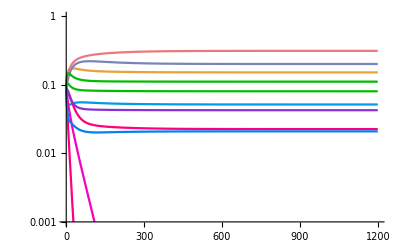

```mathematica
logSeriesPlot=LogPlot[Evaluate[Table[Indexed[sol[t],i]/l,{i,m}]],{t,0,steps},PlotRange->{{0,steps},{10^-3,1}},Ticks->{{0,300,600,900,1200},{.001,.01,.1,1}},TicksStyle->Black,PlotStyle->colors,LabelStyle->{FontSize->14}]
```

```mathematica
Export["fig1C_timeseries.svg",%,"SVG"];
```

#### strat plot for p=3

```mathematica
mapToSimplex[point_]:=
Module[{},
newX=point[[2]]-point[[1]];
newY=Sqrt[3]*point[[3]];
{newX,newY}
];
```

```mathematica
remappedStrats=Table[{mapToSimplex[α[[i]]]},{i,m}];
```

```mathematica
supplyPoint=mapToSimplex[s];
```

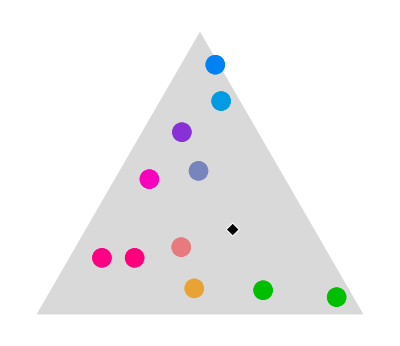

```mathematica
Show[Graphics[{LightGray,Triangle[{{-1,0},{1,0},{0,Sqrt[3]}}]}],ListPlot[remappedStrats,PlotStyle->colors,PlotMarkers->ConstantArray[{"•",20},m],PlotRange->{{-1,1},{0,Sqrt[3]}}],(*ListPlot[{{mapToSimplex[s]}},PlotStyle->Black,PlotMarkers->{"◆",19}]*)Graphics[{EdgeForm[{White}],Polygon[{supplyPoint+{-.04,0},supplyPoint+{0,.04},supplyPoint+{.04,0},supplyPoint+{0,-.04}}]}]]
```

```mathematica
Export["fig1A_strategies.svg",%,"SVG"];
```

```mathematica
c1Final=fullConcentration[sol[steps],1];
c2Final=fullConcentration[sol[steps],2];
c3Final=fullConcentration[sol[steps],3];
finalPositions=getPositions[sol[steps]];
```

### Final Concentration

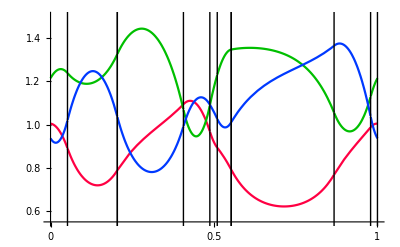

```mathematica
dividers=Table[Line[{{finalPositions[[i,2]],0},{finalPositions[[i,2]],10}}],{i,m}];
cPlot=Plot[{c1Final,c2Final,c3Final},{theta,0,l},PlotRange->{Full,{.55,1.5}},PlotStyle->{XYZColor[1,0,0],Darker[XYZColor[0,1,0],.25],XYZColor[0,0,1]},Ticks->{{{0,0},{l/2,.5},{l,1}},Automatic},TicksStyle->Black,
Epilog->{dividers},LabelStyle->{FontSize->12}]
```

```mathematica
Export["fig1D_concentrations.svg",cPlot,"SVG"];
```

### spatial time slice evolution

```mathematica
sampleTimes=Range[0,75,1];
numSamples=Length[sampleTimes];
```

```mathematica
popSamples=sol/@sampleTimes;
```

```mathematica
positionSamples=getPositions/@popSamples;
```

```mathematica
boundarySamples=Table[positionSamples[[i,j]]=positionSamples[[i,j]]//Last,{i,numSamples},{j,m}];
```

```mathematica
pairListTimeOrder=Table[Transpose[{boundarySamples[[i]],ConstantArray[sampleTimes[[i]],m]}],{i,numSamples}];
```

```mathematica
pairListSpeciesOrder=Transpose[pairListTimeOrder];
```

```mathematica
flippedPairListSpeciesOrder=Table[Reverse[pairListSpeciesOrder[[i,j]]],{i,m},{j,numSamples}];
```

```mathematica
fillingChart=Table[i->{{i-1},colors[[i]]},{i,2,m}];
fillingChart=Join[{1->{Axis,colors[[1]]}},fillingChart];
```

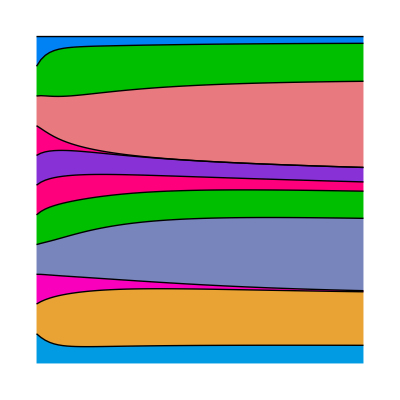

```mathematica
expA=ListLinePlot[flippedPairListSpeciesOrder,PlotStyle->Directive[Black,Thin],Filling->{fillingChart},Ticks->None,Axes->False,AspectRatio->1];
Rotate[expA,-Pi/2]
Export["fig1B_spatialtimeseries.svg",%,"SVG"];
```